Number Theory and Cryptography

## Introduction

The Wolfram Language includes numerous functions for exploring number theory. In this chapter, we will see how to use Mathematica’s computational abilities to compute and solve congruences, represent integers in bases other than 10, explore arithmetic algorithms in those bases, check whether or not a number is prime, and compute discrete logarithms. We will also see how Mathematica can help explore several of the applications described in the textbook, in particular, hashing functions, pseudorandom numbers, check digits, and, of course, cryptography.

## 4.1 Divisibility and Modular Arithmetic

In this section, we will use Mathematica to explore divisibility of integers and modular arithmetic. We will see how to compute quotients and remainders in integer division, how to test integers for the divisibility relationship, and how to perform computations in modular arithmetic. This section will conclude with an illustration of how to create infix addition and multiplication operators for modular arithmetic and a demonstration of how Mathematica can be used to compute addition and multiplication tables.

### Quotient, Remainder, and Divisibility

The Wolfram Language functions Quotient and Mod compute the quotient and remainder, respectively, obtained from dividing two integers. For example, consider 99 divided by 13.

```mathematica
Quotient[99,13]
```

7

```mathematica
Mod[99,13]
```

8

These results indicate that 99 divided by 13 results in a quotient of 7 and a remainder of 8. That is, 99=13·7+8.

Note that the textbook uses the notation a mod m to represent the remainder when a is divided by m, using mod like an operator. To enter this in Mathematica, you must use the functional notation Mod[a,m].

Another function, QuotientRemainder, produces a list with first element the quotient and second element the remainder.

```mathematica
QuotientRemainder[99,13]
```

{7,8}

#### Checking Divisibility

To test whether one integer divides another, you can, of course, check to see if the remainder is 0 or not. For example, the following shows that 3|132.

```mathematica
Mod[132,3]
```

0

The Wolfram Language also provides the function Divisible for testing divisibility. The Divisible function returns true if its first argument is divisible by the second.

```mathematica
Divisible[132,3]
```

True

```mathematica
Divisible[99,13]
```

False

#### Offset

Recall from the division algorithm that the remainder must always be nonnegative, even when the dividend is negative. The Mod function respects that convention by default, with Mod[a,m] returning a value between 0 and m-1.

```mathematica
Mod[-27,5]
```

3

However, there are times when it is more useful to allow negative values. For example, consider the following question: “It is now 11:00 A.M. What time will it be 142 hours from now?” If we compute 142 mod 24,

```mathematica
Mod[142,24]
```

22

We see that the time will be the same 142 hours from now as 22 hours from now. It is also the case that 142≡-2 (mod 24), which means that the time 142 hours from now is the same as the time 2 hours earlier, that is, 9:00 A.M. You can see that this congruence is somewhat more convenient.

To support this, the Mod function accepts an optional third argument, called the offset. The offset specifies a lower bound on the Mod function’s output. Specifically, for an integral offset d, Mod[a,m,d] will return the value congruent to a mod m that lies between d and d+m-1. For example, by specifying an offset of 1, the result will be between 1 and m, so a computation that would ordinarily return 0 will return the value of the modulus instead.

```mathematica
Mod[132,3,1]
```

3

The value 1 is a common offset, as it ensures a positive result that can then be used as an index into a list. Another common offset is the fraction -m/2. This offset ensures that the output is the integer closest to 0 that is congruent to the first argument modulo the second. For example, returning to the time example above, to obtain the result -2 we use the offset -24/2.

```mathematica
Mod[142,24,-24/2]
```

-2

### Congruences

The first argument to Mod can be any algebraic expression. For example, you can compute 3+4·9^2mod 5 as follows.

```mathematica
Mod[3+4*9^2,5]
```

2

To test a congruence, for example to confirm that 428≡530 (mod 17), you must apply the Mod function to both values and test them using the Equal (==) relation.

```mathematica
Mod[428,17]==Mod[530,17]
```

True

You may not include the Equal (==) relation within the argument to Mod.

#### Solving Congruences

Mathematica can solve congruences by using the Solve function in conjunction with the Modulus option. To do so, give the congruence or list of simultaneous congruences as the first argument to Solve and identify the modulus using the Modulus option. As an example, consider Exercise 17a from Section 4.1 of the textbook. Under the assumption that a≡4 (mod 13), we are to solve c≡9a (mod 13). We solve this using Mathematica as follows.

```mathematica
Solve[{a==4,c==9*a},Modulus->13]
```

{{a→4,c→10}}

Note that the congruences are entered as a list. This indicates that they must be simultaneously satisfied. Also note that we must use the Equal (==) relation, not Set (=), when specifying the congruences.

If there are no solutions to the congruence, then Solve will return the empty list.

```mathematica
Solve[n^2==3,Modulus->4]
```

{}

### Arithmetic Modulo m

In this subsection, we will define operators based on the definitions of +_m and ·_m given in the text. Our goal will be to get as close as possible to being able to enter 7+_11 9 and have Mathematica return 5.

The usual style of writing arithmetic operators in between the operands is referred to as infix notation. There are operators that Mathematica recognizes as infix operators, but which do not have built-in definitions. We can take advantage of this to create our own infix operators by providing definitions for these undefined operators.

You can see all of the operators in the Wolfram Language in the table of operator precedence in the Operator Input Forms tutorial. Those operators with a triangular mark in the far right of the table have built-in definitions. Those without such a mark are available for your own use. Here, we will make use of the CirclePlus (⊕) and CircleTimes (⊗) operators.

To enter these as infix operators, you need to use their aliases. To enter ⊕, type Escc+Esc, and to enter ⊗, type Escc*Esc.

Observe that if you enter an expression using one of the operators, and apply the FullForm function, you can see that Mathematica interprets the infix operator as an application of the named function.

```mathematica
2⊕3//FullForm
```

CirclePlus[2,3]

In addition, note that while these functions are currently undefined, they do have a defined precedence. For example, 2⊕3⊗4 is interpreted as 2⊕(3⊗4), which can be verified by inspecting the functional expression obtained with FullForm.

```mathematica
2⊕3⊗4//FullForm
```

CirclePlus[2,CircleTimes[3,4]]

To define the operator, you can issue the definition using either the functional or infix form. Below, we define addition in functional form and multiplication in infix form. Regardless of the form you provide the definition, Mathematica will properly evaluate both forms.

```mathematica
CirclePlus[a_,b_]:=Mod[a+b,11]
```

```mathematica
a_⊗b_:=Mod[a*b,11]
```

We can now compute 7+_11 9 and 3·_11 5 using the ⊕ and ⊗ operators.

```mathematica
7⊕9
```

5

```mathematica
3⊗5
```

4

### Addition and Multiplication Tables

We conclude this section by producing addition and multiplication tables.

We will create the tables, unsurprisingly, using the Table function. The first argument will be the sum or product of two variables within the Mod function. The Table repetition arguments will specify that the variables range from 0 to one less than the modulus. A call to TableForm will make the result readable.

Here is the addition table modulo 5.

```mathematica
Table[Mod[a+b,5],{a,0,4},{b,0,4}]//TableForm
```

0 | 1 | 2 | 3 | 4
1 | 2 | 3 | 4 | 0
2 | 3 | 4 | 0 | 1
3 | 4 | 0 | 1 | 2
4 | 0 | 1 | 2 | 3

We can improve the table a bit more by adding column and row headings. This is done with the TableHeadings option. By setting the TableHeadings option to a list consisting of two sublists corresponding to the desired labels for the rows and then the columns, Mathematica will display those labels as headings. The keyword None can be used in place of one of the sublists if you wanted to omit the corresponding set of labels.

```mathematica
TableForm[Table[Mod[a+b,5],{a,0,4},{b,0,4}],TableHeadings->{{0,1,2,3,4},{0,1,2,3,4}}]
```

| 0 | 1 | 2 | 3 | 4
0 | 0 | 1 | 2 | 3 | 4
1 | 1 | 2 | 3 | 4 | 0
2 | 2 | 3 | 4 | 0 | 1
3 | 3 | 4 | 0 | 1 | 2
4 | 4 | 0 | 1 | 2 | 3

Using that example as a model, it is easy to create general functions that will accept a modulus and display the addition or multiplication table.

```mathematica
AdditionTable[m_]:=Module[{a,b},
TableForm[Table[Mod[a+b,m],{a,0,m-1},{b,0,m-1}],
TableHeadings->{Range[0,m-1],Range[0,m-1]}]]
```

```mathematica
MultiplicationTable[m_]:=Module[{a,b},
TableForm[Table[Mod[a*b,m],{a,0,m-1},{b,0,m-1}],
TableHeadings->{Range[0,m-1],Range[0,m-1]}]]
```

Here is the multiplication table modulo 5.

```mathematica
MultiplicationTable[5]
```

| 0 | 1 | 2 | 3 | 4
0 | 0 | 0 | 0 | 0 | 0
1 | 0 | 1 | 2 | 3 | 4
2 | 0 | 2 | 4 | 1 | 3
3 | 0 | 3 | 1 | 4 | 2
4 | 0 | 4 | 3 | 2 | 1

## 4.2 Integer Representations and Algorithms

In this section, we will see how Mathematica can be used to explore representations of integers in various bases and to explore algorithms for computing with integers. We will begin by looking at the Wolfram Language’s built-in functions for converting between bases. Then, we will focus our attention on binary representations of integers and how to implement algorithms for addition and multiplication on binary representations. We restrict our attention to positive integers throughout this section.

### Base Conversion

The Wolfram Language provides support for converting from one base representation to another via the functions IntegerDigits, IntegerString, and FromDigits.

The IntegerDigits function is used to convert a positive integer, expressed in base 10, into a list of the digits of the integer expressed in a specified base. The first argument to IntegerDigits is the base 10 integer. If no other arguments are provided, the function returns the list of the digits of the integer.

```mathematica
IntegerDigits[1234]
```

{1,2,3,4}

Note that the most significant digit is first in the list and the least significant is last. That is, the “one’s digit” is the last element in the list.

By providing a base as a second argument, the IntegerDigits function will output the list of the digits in the representation of the integer in that base. The following indicates that (1234)_10=(103102)_4.

```mathematica
IntegerDigits[1234,4]
```

{1,0,3,1,0,2}

For bases larger than 10, IntegerDigits does not make use of letters for digits with values larger than 9. Rather, it uses the base 10 representation of the value of such digits. For example, in Example 5 of the textbook, it is shown that (177130)_10=(2B3EA)_16. The output of IntegerDigits reports 10, 11, and 14 rather than A, B, and E.

```mathematica
IntegerDigits[177130,16]
```

{2,11,3,14,10}

The IntegerDigits function also accepts a third argument to specify a minimum length of the output. If the representation of the integer in the given base has fewer digits than specified by the third argument, zeros will be added on the left. The following shows the representation of 123 in binary (base 2), with ten digits.

```mathematica
IntegerDigits[123,2,10]
```

{0,0,0,1,1,1,1,0,1,1}

The IntegerString function is very similar to IntegerDigits, accepting the same arguments and having a very similar effect. The difference is that the output of IntegerString is a string rather than a list. This means that the output has a more typical appearance. Contrast the output below to the corresponding example above.

```mathematica
IntegerString[1234,4]
```

103102

Note that, despite appearances, the output is in fact a string object and not a numerical object.

```mathematica
Head[%]
```

String

As a result, you cannot manipulate the output of IntegerString using numerical operators. The IntegerDigits function is much more useful if you wish to work with the output. However, IntegerString produces much more readable output. It also follows the usual convention of using letters for digits larger than 9.

```mathematica
IntegerString[177130,16]
```

2b3ea

The IntegerDigits and IntegerString functions are both used to take a base 10 representation of a positive integer and return a representation in another base. For the reverse, we use the FromDigits function.

The first argument of FromDigits can be either a list, like the output of IntegerDigits, or a string, like the output of IntegerString. With no second argument, Mathematica will assume that the input is intended to be base 10 and will convert the list or string into the corresponding integer.

```mathematica
FromDigits[{1,2,3,4}]
```

1234

```mathematica
FromDigits["1234"]
```

1234

The second argument specifies the base in which the first argument is given. For example, to convert (103012)_4 back to base 10, you enter either of the following.

```mathematica
FromDigits[{1,0,3,1,0,2},4]
```

1234

```mathematica
FromDigits["103102",4]
```

1234

For bases larger than 10, you can use letters to represent digits larger than nine when using a string as the first argument to FromDigits. Note that either lower or upper case is acceptable.

```mathematica
FromDigits["2B3EA",16]
```

177130

Finally, note that both IntegerString and FromDigits can, in place of the base, accept “Roman”, in which case the function will convert to or from a Roman numeral representation.

```mathematica
IntegerString[2013,"Roman"]
```

MMXIII

```mathematica
FromDigits["MMXIII","Roman"]
```

2013

The BaseForm function should also be mentioned. Unlike the functions above, BaseForm only affects how a number is displayed by Mathematica, not its type. That is, BaseForm does not change an integer into a list or string, it only displays the number as if it were in a different base. Its arguments are a base 10 integer and a base.

```mathematica
BaseForm[177130,16]
```

(2b3ea)_16

In the other direction, you can use the double-caret (^^) notation to enter a number in a specified base. Enter the base, followed by the representation of the number in that base. For example, to enter (A3)_16 you type the following.

```mathematica
16^^a3
```

163

#### Converting Between Two Non-10 Bases

Given a positive integer in a base other than 10, you can convert it to another by using base 10 as an intermediary. For example, to convert (123)_5 to base 3, you proceed as follows. First, convert to base 10 using FromDigits.

```mathematica
FromDigits["123",5]
```

38

Then, use IntegerString to convert to base 3.

```mathematica
IntegerString[38,3]
```

1102

The result indicates that (123)_5=(1102)_3.

We can combine these two steps into a single function that takes three arguments: a string representing the integer, the starting base, and the final base. The body of the function is simply a composition of FromDigits and IntegerString.

```mathematica
convertString[n_,b1_,b2_]:=IntegerString[FromDigits[n,b1],b2]
```

```mathematica
convertString["123",5,3]
```

1102

It is left to the reader to define a similar function that outputs a list of digits rather than a string.

### Binary Addition

In this subsection, we will implement Algorithm 2 from Section 4.2, addition of integers. Our function will accept two binary representations given as lists of 0s and 1s with the most significant digit first. The first task for our function will be to make sure that the binary representations are of the same length. To do this, we compute the maximum of the lengths of the two lists, which will be stored as n, and then add as many 0s to the shorter list as are necessary to make both lists that length. We also initialize a sum list S to the list of that same length consisting of all 0s.

To add 0s to the input list, we use the PadLeft function, which takes a list and a length and returns the list of the desired length obtained by adding 0s on the left side of the list. As you might suspect, there is also a PadRight function. To initialize S, we use ConstantArray, which, given an expression and a length creates the list of the desired length all of whose elements are the given expression. We illustrate these functions below.

```mathematica
PadLeft[{1,2,3},7]
```

{0,0,0,0,1,2,3}

```mathematica
ConstantArray["x",5]
```

{x,x,x,x,x}

Once these initial tasks are completed, we follow Algorithm 2. Note that the indices used must be modified to match that used by the Wolfram Language. The loop variable j, as presented in the textbook, ranges from 0 to n-1, where 0 is the index of the least significant (the “one’s”) digit and n-1 is the index of the most significant digit. In this implementation, the least significant digit in the input values, A and B, will be in the last position, which has index equal to their length, n. The most significant digit will be in position 1. Consequently, our For loop will have variable j ranging from n to 1.

The last difference between our implementation and Algorithm 2 is the use of the PrependTo function to add a 1 at the beginning of the sum, in case a carry requires the result have an additional digit.

```mathematica
addition[a_List,b_List]:=Module[{n,A,B,S,c,j,d},
n=Max[Length[a],Length[b]];
A=PadLeft[a,n];
B=PadLeft[b,n];
S=ConstantArray[0,n];
c=0;
For[j=n,j≥1,j--,
d=Floor[(A[[j]]+B[[j]]+c)/2];
S[[j]]=A[[j]]+B[[j]]+c-2*d;
c=d
];
If[c==1,PrependTo[S,1]];
S
]
```

```mathematica
addition[{1,0,1,0},{1,1,1,0,1,0}]
```

{1,0,0,0,1,0,0}

### Binary Multiplication

Finally, we will implement a multiplication algorithm, presented as Algorithm 3 in Section 4.2. Once again, our function will accept the binary representations of positive integers as the inputs. This time, however, it is not necessary for them to have the same length.

The shift that occurs when b_j=1 is illustrated by the following example. To shift the list {1,1,1,1} by five places, we must add five 0s at the end of the list. We do this by using ConstantArray to create the list of five 0s and then Join to combine the original list with this list of 0s.

```mathematica
shiftExample={1,1,1,1}
```

{1,1,1,1}

```mathematica
Join[shiftExample,ConstantArray[0,5]]
```

{1,1,1,1,0,0,0,0,0}

We will store the partial products using an indexed variable. Recall from Section 2.4 of this manual that we can store an object in an indexed variable, c, by making an assignment to the symbol c[i] for index i.

The product p will be initialized to {0}, a binary representation of 0. The addition in the final loop will be performed by the addition function we created above.

As noted above, there is a discrepancy between the way indices are used in the pseudocode in the text and the indices used in Mathematica. For this function, we will mirror the textbook with the loop variable j ranging from 0 to n-1, where n is the number of digits in the second number. We interpret j as being the number of digits beyond the least significant digit, which has position n. Within the body of the loop, we inspect location n-j.

Here is our implementation of Algorithm 3.

```mathematica
multiplication[a_List,b_List]:=Module[{n,j,c,p},
n=Length[b];
For[j=0,j≤n-1,j++,
If[b[[n-j]]==1,
c[j]=Join[a,ConstantArray[0,j]],
c[j]={0}
]
];
p={0};
For[j=0,j≤n-1,j++,
p=addition[p,c[j]]
];
p
]
```

We test our function using Example 10 from Section 4.2.

```mathematica
multiplication[{1,1,0},{1,0,1}]
```

{1,1,1,1,0}

## 4.3 Primes and Greatest Common Divisors

In this section, we will see how to use Mathematica to find primes, find prime factorizations, and compute greatest common divisors and least common multiples. We will also use Mathematica’s capabilities to explore the distribution of primes.

### Primes

We will first introduce some of the Wolfram Language’s functions for testing whether a number is prime and for finding primes.

#### Testing for Primality

The PrimeQ function accepts a single argument, an integer to be tested, and returns true or false.

```mathematica
PrimeQ[5]
```

True

```mathematica
PrimeQ[10]
```

False

```mathematica
PrimeQ[2^13-1]
```

True

Unlike the trial division algorithm discussed in the book, which checks all possible divisors to see if a number is prime or composite, PrimeQ uses a probabilistic primality test. This probabilistic test gains much faster performance at the cost of a small possibility that the command will return an incorrect result. There is no known example of an integer for which PrimeQ is incorrect and any such example must be exceptionally large. Therefore, despite there being a chance of error, PrimeQ is in fact very reliable.

#### Listing Primes

The function Prime accepts as input a positive integer i and outputs the ith prime number.

```mathematica
Prime[1]
```

2

```mathematica
Prime[2]
```

3

```mathematica
Table[Prime[i],{i,20}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71}

```mathematica
Prime[100000]
```

1299709

The Wolfram Language also includes the NextPrime function, which returns the smallest prime larger than the input value. For example, to find the first prime number larger than 1000, enter the following.

```mathematica
NextPrime[1000]
```

1009

The NextPrime function can also be given an optional second argument, which must be an integer. NextPrime[n,k] returns the kth prime larger than n. If the second argument is negative, the function instead returns the prime smaller than n. For example, the following expressions find the third prime after 1000 and the prime before it.

```mathematica
NextPrime[1000,3]
```

1019

```mathematica
NextPrime[1000,-1]
```

997

### Prime Factorization

To compute the prime factorization of an integer, we can use the function FactorInteger.

```mathematica
FactorInteger[100]
```

{{2,2},{5,2}}

```mathematica
FactorInteger[123456789]
```

{{3,2},{3607,1},{3803,1}}

```mathematica
FactorInteger[-987654321]
```

{{-1,1},{3,2},{17,2},{379721,1}}

The output of FactorInteger is a list of pairs. Each pair consists of a prime number and the multiplicity, or exponent, of that prime in the prime factorization. Note that in the last example, with negative input, one of the members of the list is the pair {-1,1}, indicating that (-1)^1 is in the factorization. The outputs above indicate that 100=2^2·5^2, 123456789=3^2·3607^1·3803^1, and -987654321=(-1)^1·3^2·17^2·379721^1.

Note that FactorInteger can also accept an optional argument to limit the effort Mathematica will exert in trying to factor. Entering Automatic as the second argument limits the function to factors that it can find easily. You can also give a positive integer as the second argument, and Mathematica will then find at most that many distinct factors.

```mathematica
FactorInteger[236914830635411777378758175934586404476822]
```

{{2,1},{197,1},{509,1},{10459723,3},{32129861,2}}

```mathematica
FactorInteger[236914830635411777378758175934586404476822,3]
```

{{394,1},{509,1},{1181349070215370924270532326421800507,1}}

The first expression above factors the given integer into its complete prime factorization. The second is limited to finding only three distinct factors. After finding the first two prime factors, 394 and 509, it reports the remainder as the last factor with exponent 1. This gives you a way to have Mathematica only perform the easy parts of factorizations, which can help ensure that your functions run quickly during development. Then, when you are ready to let the function take all the time it needs, you can remove the limitation.

### The Distribution of Primes

The Prime Number Theorem (Theorem 4 in Section 4.3 of the text) tells us that the number of primes not exceeding x is approximated by the function x/(ln x). In this subsection, we will use Mathematica’s graphing capabilities to graph the number of primes not exceeding x.

Recall from Section 3.3 of this manual that we can graph a list of points by using the ListPlot function applied to a list of x–y pairs. Our x values will be the integers from 2 to 1000 (we omit 1 since there are no primes less than or equal to 1).

To find the number of primes not exceeding x, we use the function PrimePi. The expression π(x) is the standard notation for the number of primes less than or equal to x. The symbol PrimePi distinguishes this function in the Wolfram Language from the mathematical constant, which is given the symbol Pi. To calculate the number of primes less than or equal to 1000, for example, we enter the following.

```mathematica
PrimePi[1000]
```

168

We use the Table function to produce the list of pairs {x,π(x)}, which we will graph.

```mathematica
piList=Table[{x,PrimePi[x]},{x,1000}];
```

As we did in the solution to Computer Project 10 of Chapter 3, we will graphically compare the values of π(x) to the function x/(ln x). We will define two graphics objects and then combine them with the Show function. Refer to Chapter 3 of this manual, particularly Section 3.3 and the solution to Computer Project 10, for detailed information about the commands ListPlot and Plot that we use here.

We also use the legending functions Legended and LineLegend. For a single application of Plot, you can use the PlotLegends option to very easily add a legend to the plot. That option is not available to Show, however. Instead, you must use the more general function Legended and manually construct the legend with LineLegend (or one of the related functions such as PointLegend or SwatchLegend). In this context, Legended can be thought of as a wrapper containing a graphics object, or more precisely an expression that produces a graphics object, as the first argument, and a call to a function that creates a legend as the second argument. The LineLegend function generally takes two arguments: first a list of colors and second a list of labels for the color in the corresponding position.

```mathematica
piPlot=ListPlot[piList,PlotStyle->Blue];
```

```mathematica
xlnxPlot=Plot[x/Log[x],{x,2,1000},PlotStyle->Red];
```

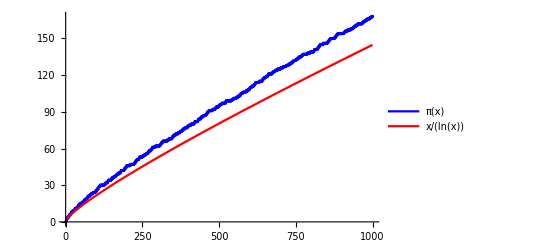

```mathematica
Legended[Show[piPlot,xlnxPlot],LineLegend[{Blue,Red},{"π(x)","x/(ln(x))"}]]
```

Notice that while the blue line representing π(x) seems to remain above the red line representing x/(ln x), it is fairly clear from the graph that they grow at similar rates.

### Greatest Common Divisor and Least Common Multiple

The Wolfram Language provides the functions GCD and LCM for computing the greatest common divisor and the least common multiple of integers. To compute the greatest common divisor of two integers, you apply the GCD function to them.

```mathematica
GCD[6,9]
```

3

You can also compute the greatest common divisor of more than two integers. For more than two integers, the greatest common divisor is defined to be the largest integer that is a divisor of all of them. For example, 3 divides 6, 9, and 12, so:

```mathematica
GCD[6,9,12]
```

3

The LCM command finds the least common multiple of two or more integers. For example,

```mathematica
LCM[6,9]
```

18

```mathematica
LCM[12,18,33]
```

396

#### Relatively Prime

Recall from the text that two numbers are said to be relatively prime if their greatest common divisor is 1. For example, consider 10 and 21.

```mathematica
GCD[10,21]
```

1

Since GCD returned 1, we conclude that 10 and 21 are relatively prime.

The Wolfram Language function CoprimeQ, applied to two integers, returns true if they are relatively prime and false if not.

```mathematica
CoprimeQ[3,6]
```

False

```mathematica
CoprimeQ[22,15]
```

True

Also recall that a list of integers a_1,a_2,…,a_n are said to be pairwise relatively prime if gcd(a_i,a_j)=1 whenever 1≤i<j≤n. That is, when every pair is relatively prime. The CoprimeQ function, applied to more than two integers, tests this property.

Observe that 14, 39, and 55 are pairwise relatively prime.

```mathematica
CoprimeQ[14,39,55]
```

True

However, 42, 165, and 182 are not pairwise relatively prime, since 42 and 182 are both even, even though the common GCD of all three integers is 1.

```mathematica
GCD[42,165,182]
```

1

```mathematica
CoprimeQ[42,165,182]
```

False

#### The Extended Euclidean Algorithm

While GCD is useful for calculating the greatest common divisor of integers, it is sometimes desirable to be able to express the greatest common divisor as an integral combination of the integers. Specifically, given integers a and b, we may wish to express gcd(a,b) as s·a+t·b where s and t are integers. The fact that such integers always exist is known as Bézout’s Theorem, given in the text as Theorem 6 of Section 4.3. Following Theorem 6, the text describes the extended Euclidean algorithm, which produces not only the greatest common divisor but also the integers s and t, called the Bézout coefficients.

In the Wolfram Language, the function ExtendedGCD is an implementation of the extended Euclidean algorithm. This function accepts two or more integers as arguments. It returns a list whose first element is the greatest common divisor of the arguments and whose second element is a sublist whose members are the Bézout coefficients. As an example, consider 252 and 198, the values used in Example 17 of the textbook.

```mathematica
ExtendedGCD[252,198]
```

{18,{4,-5}}

The results above indicate that gcd(252,198)=18=4·252-5·198. Note that the order of the coefficients is the same as the order of the arguments to the function.

## 4.4 Solving Congruences

In this section, we will see how Mathematica can be used to solve congruences. We will begin the section by looking at how to find inverses and solve linear congruences. We will then consider the Chinese Remainder Theorem. Next, we will use Mathematica to find pseudoprimes, and we conclude with an exploration of primitive roots and discrete logarithms.

### Modular Inverses

Example 1 of Section 4.4 of the text demonstrates how Bézout coefficients can be used to find the inverse of an integer modulo a number. In the previous section of this manual, we saw that the ExtendedGCD function can be used to obtain the Bézout coefficients.

#### Finding Inverses with ExtendedGCD

For example, to find the inverse of 264 modulo 3185, we need to find s so that s·264+t·3185=1, provided that 264 and 3185 are relatively prime.

Recall that ExtendedGCD applied to two integers returns a structure of the form {gcd,{s,t}} where gcd is the greatest common divisor of the two integers, and s and t are the Bézout coefficients. Knowing that this is always the form of the output, Mathematica allows us to assign the result of ExtendedGCD to a structure of that form. This has the effect of assigning the symbols to the corresponding numbers in the output.

```mathematica
{gBezout,{sBezout,tBezout}}=ExtendedGCD[264,3185]
```

{1,{374,-31}}

Since the first element is 1, we know that 264 and 3185 are relatively prime. In addition, the assignment has caused the Bézout coefficients to be stored in the symbols.

```mathematica
sBezout
```

374

```mathematica
tBezout
```

-31

This indicates that 1=374·264+(-31)·3185. And thus, 374 is the inverse of 264 modulo 3185. We can confirm this by computing the product modulo 3185.

```mathematica
Mod[374*264,3185]
```

1

#### Finding Inverses with PowerMod

The Wolfram Language provides a simpler way to compute the modular inverse. The textbook uses the notation ā to indicate the modular inverse of an integer. An alternate notation is a^-1, which calls to mind the notation used for reciprocals, as in 3^-1=1/3.

The PowerMod function computes powers of integers in modular arithmetic. It takes three arguments: the base integer, the exponent, and the modulus. For example, the following computes 3^4 (mod 5).

```mathematica
PowerMod[3,4,5]
```

1

For positive exponents, PowerMod is more efficient than applying Mod with the exponent computed in the argument. Moreover, PowerMod accepts negative (and even rational) exponents. In particular, applying PowerMod with second argument -1 computes the modular inverse.

```mathematica
PowerMod[264,-1,3185]
```

374

Note that if the integer and the modulus are not relatively prime, no inverse exists and an error is generated.

```mathematica
PowerMod[4,-1,10]
```

PowerMod::ninv: 4 is not invertible modulo 10.

PowerMod[4,-1,10]

#### Solving Congruences

We saw in Section 4.1 of this manual that the Solve function with Modulus option can be used for solving congruences. We can use this command to solve linear congruences such as 4x≡3 (mod 11).

```mathematica
Solve[4*x==3,Modulus->11]
```

{{x→9}}

The first argument to Solve is the congruence expressed with an Equal (==) symbol. Following the equation is a rule setting the Modulus option to the modulus value. Mathematica returns a list whose elements express the solutions to the congruence. If there is no solution, Mathematica returns the empty list.

The following attempts to solve 4x≡1 (mod 10), which is the same as finding an inverse for 4 modulo 10 and has no solution.

```mathematica
Solve[4*x==1,Modulus->10]
```

{}

It is also possible to have multiple solutions. For example, 3x≡9 (mod 12).

```mathematica
Solve[3*x==9,Modulus->12]
```

{{x→3+4 C[1]}}

The symbol C[1] is used in the Wolfram Language to represent an arbitrary integer. This output indicates that any value of x of the form 3+4·C will solve the congruence. We can obtain a specific solution by substituting a particular integer for the symbol C[1], using ReplaceAll (/.).

```mathematica
Solve[3*x==9,Modulus->12]/.C[1]->1
```

{{x→7}}

### The Chinese Remainder Theorem

The text describes two approaches to solving systems of congruences of the form

x≡a_1 (mod m_1)
x≡a_2 (mod m_2)
             ⋮
x≡a_n (mod m_n)

The Wolfram Language provides an implementation of the Chinese remainder theorem, ChineseRemainder. The function takes two arguments: a list of the values {a_1,a_2,…,a_n} first and a list of the moduli {m_1,m_2,…,m_n} second. The result is the smallest positive integer that satisfies all of the congruences. As an example, we solve the congruences

x≡2 (mod 3)
x≡4 (mod 5)
x≡6 (mod 7)
x≡10 (mod 11)

```mathematica
ChineseRemainder[{2,4,6,10},{3,5,7,11}]
```

1154

#### Creating a Function

We will create a function for solving systems of congruences. This implementation will be based on the construction given in the proof of the Chinese remainder theorem. Although this will be less efficient than the built-in ChineseRemainder function, implementing the algorithm can help you to better understand the proof of the theorem.

Our function, which we call crTheorem, will accept the same arguments as ChineseRemainder: two lists, a and m, representing the values and the moduli of the congruences. It will begin with two tests to check that the lists are the same length and that the moduli are in fact pairwise relatively prime, as is required by the assumptions of the theorem. We use CoprimeQ, described in Section 4.3 of this manual, to check that the moduli are pairwise relatively prime. If these tests fail, the following messages are generated.

```mathematica
crTheorem::argsize="Arguments must be lists of the same size.";
```

```mathematica
crTheorem::argcp="Moduli must be pairwise relatively prime.";
```

We will embed the tests inside a small function in order to make the crTheorem function easier to read.

```mathematica
crTestArgs[a_,m_]:=Check[
If[Length[a]≠Length[m],Message[crTheorem::argsize]];
If[Not[Apply[CoprimeQ,m]],Message[crTheorem::argcp]];
True,
False]
```

Most of the work of crTestArgs is done in the two If statements. The first compares the lengths of a and m and the second checks whether the moduli are relatively prime. If the lists are of different lengths or the moduli are not relatively prime, the appropriate message is issued. Note that the Apply function is used in the second If statement in order to apply the function CoprimeQ, which expects integer arguments, to the list m.

The Check function is used to “listen” for messages. It evaluates its first argument, which in this case is the three lines ending with the expression True. If no messages are generated, then the result of the Check is the outcome of that evaluation. In this case, if the two If statements do not raise messages, then the outcome of the Check is True. However, if any messages are raised while evaluating the first argument to Check, then Check returns its second argument instead. In this case, this means that if any messages are raised, then the result of the function will be False.

As you can see below, with valid input, crTestArgs results in True, and produces both error messages and returns False for arguments that violate the rules.

```mathematica
crTestArgs[{1,2,3},{5,7,11}]
```

True

```mathematica
crTestArgs[{1,2},{4,5,6}]
```

crTheorem::argsize: Arguments must be lists of the same size.

crTheorem::argcp: Moduli must be pairwise relatively prime.

False

When we define the crTheorem function, we will use patterns in the arguments to ensure that the arguments are lists of integers, and we will give crTestArgs as a Condition (/;), as shown below.

crTheorem[a:{__Integer},m:{__Integer}]/;crTestArgs[a,m]:=...

The syntax a:{__Integer}, and likewise for m, names the argument and imposes the pattern that it be a sequence of integers enclosed in braces, that is, a list of integers. On the right hand side of the Condition (/;) operator, we apply crTestArgs to the arguments before the SetDelayed (:=) operator. With a function definition of this form, when you enter a call to crTheorem, Mathematica will first check to see that the arguments match the specified patterns. If not, for instance if you provide a different number of arguments or attempt to use anything other than two lists of integers, Mathematica will simply return the expression unevaluated. Assuming that you enter two lists of integers, then Mathematica will apply crTestArgs. If this function returns False, then Mathematica will return the crTheorem call unevaluated. Moreover, in this case, Mathematica will not attempt to evaluate the body of the function. Only after the arguments have matched the pattern and crTestArgs has returned True, will Mathematica evaluate the body of the function definition.

While the above is a bit more complicated seeming than placing the tests in the body of the function and causing them to terminate execution with a Return or an Abort, it is a more elegant way to ensure that the function is robust.

Turning now to the main work of crTheorem, it begins by setting p equal to the product of the moduli. (Note that p corresponds to m in the statement of the theorem in the text. This is the only notational difference between the function defined here and the text.) Note that we use the Apply (@@) operator with the Times (*) function in order to compute this product. Times (*) is the functional version of the multiplication operator and combining it with Apply (@@) results in the product of the elements of the list m.

The function then needs to compute M_k and y_k. We use the indexed variables M and y for this. Note that this creates a subtle syntactic point to pay attention to. Specifically, the third element of the list m is accessed via m[[3]], while M_3 is referred to by M[3]. The values are computed within a For loop. The values for M are calculated by the formula M_k=P/m_k. For y, we use the fact that the y_k are the inverses of M_k modulo m_k. That is, y_k≡M_k^-1 (mod m_k). Finally, we compute the result x=a_1 M_1 y_1+a_2 M_2 y_2+⋯+a_n M_n y_n using the Sum function and return x (mod p). Here is the function.

```mathematica
crTheorem[a:{__Integer},m:{__Integer}]/;crTestArgs[a,m]:=
Module[{p,M,y,i,x},
p=Times@@m;
For[i=1,i≤Length[a],i++,
M[i]=p/m[[i]];
y[i]=PowerMod[M[i],-1,m[[i]]]
];
x=Sum[a[[i]]*M[i]*y[i],{i,Length[a]}];
Mod[x,p] 
]
```

Observe that our function produces the same result as ChineseRemainder did above.

```mathematica
crTheorem[{2,4,6,10},{3,5,7,11}]
```

1154

### Pseudoprimes

Recall from the text that a pseudoprime to the base b is a composite number n such that b^(n-1)≡1 (mod n). We will write a function to find pseudoprimes. Our function will accept two arguments, the base b and a maximum value for n, and will return a list of the pseudoprimes that it identifies.

The algorithm is fairly straightforward. We will use a For loop beginning at 3, ending with the specified maximum and increasing by 2 each time (so as to skip even integers). Within the loop, we test whether the congruence holds and whether the number is composite, using CompositeQ. Note that if the congruence fails, Mathematica will not bother testing primality. If the integer is composite, then Sow is invoked. The Reap surrounding the loop collects the pseudoprimes into a list. As we have done in the past, we use [[2,1]] to access the list of pseudoprimes without the additional information produced by Reap.

```mathematica
findPseudoprimes[b_Integer,max_Integer]:=Module[{n},
Reap[
For[n=3,n≤max,n=n+2,
If[PowerMod[b,n-1,n]==1&&CompositeQ[n],Sow[n]]
]
][[2,1]]
]
```

Note that we used the PowerMod function rather than the Power (^) operator. The PowerMod function performs modular exponentiation intelligently, using techniques such as those discussed in Section 4.2 of the text for performing efficient modular exponentiation.

Here are the pseudoprimes to the base 2 up to 100000.

```mathematica
findPseudoprimes[2,100000]
```

{341,561,645,1105,1387,1729,1905,2047,2465,2701,2821,3277,4033,4369,4371,4681,5461,6601,7957,8321,8481,8911,10261,10585,11305,12801,13741,13747,13981,14491,15709,15841,16705,18705,18721,19951,23001,23377,25761,29341,30121,30889,31417,31609,31621,33153,34945,35333,39865,41041,41665,42799,46657,49141,49981,52633,55245,57421,60701,60787,62745,63973,65077,65281,68101,72885,74665,75361,80581,83333,83665,85489,87249,88357,88561,90751,91001,93961}

### Primitive Roots and Discrete Logarithms

The Wolfram Language includes several functions for computing primitive roots and discrete logarithms.

#### Primitive Roots

The Wolfram Language function PrimitiveRoot computes primitive roots. It takes a single argument, the modulus, and returns the smallest positive primitive root for that modulus. For example, the smallest positive primitive root of 13 is 2.

```mathematica
PrimitiveRoot[13]
```

2

Note that the PrimitiveRoot function applies to some nonprime moduli as well. The Wolfram Language uses a definition of primitive root that is more general than the definition in the text. Specifically, an integer r is a primitive root modulo an integer n if every positive integer that is both less than n and relatively prime to n can be obtained as a power of r.

The Wolfram Language function PrimitiveRootList will generate a list of all primitive roots. However, it can be informative to build our own such function, which we will do by making use of the MultiplicativeOrder function. The multiplicative order of r modulo p is defined to be the smallest positive integer m such that r^m≡1 (mod p). Equivalently, one can say that the multiplicative order of r modulo p is the number of distinct powers of r, that is, the number of different values of r^k mod p. We leave it to the reader to prove the equivalence.

The MultiplicativeOrder function accepts the element and modulus as arguments and returns the multiplicative order. For example, to compute the multiplicative order of 8 modulo 13, enter the following.

```mathematica
MultiplicativeOrder[8,13]
```

4

We conclude from this that 8^1 (mod 13), 8^2 (mod 13), 8^3 (mod 13), and 8^4 (mod 13) are all distinct, with 8^4≡1(mod 13), but that 8^5≡8^1 (mod 13). We can verify this by computing the values.

```mathematica
Table[PowerMod[8,k,13],{k,4}]
```

{8,12,5,1}

```mathematica
PowerMod[8,5,13]
```

8

Recall from Definition 3 of the textbook that a primitive root modulo a prime p is an integer r such that every nonzero element of Z_p is a power of r. Since there are p elements of Z_p, there are p-1 nonzero elements. Consequently, being a primitive root modulo a prime p is identical to having multiplicative order p-1. The fact that, as we calculated above, the multiplicative order of 8 modulo 13 is 4, not 13-1=12 implies that 8 is not a primitive root modulo 13. However, 6 has multiplicative order 12 modulo 13.

```mathematica
MultiplicativeOrder[6,13]
```

12

Consequently, 6 is a primitive root modulo 13.

To summarize, for r to be a primitive root modulo a prime p, it is necessary and sufficient that the multiplicative order of r modulo p be equal to p-1. This observation provides us with a convenient way to list all of the primitive roots for a given prime. We just consider each possible r from 2 to p-1 and calculate their multiplicative order with MultiplicativeOrder. Those whose order is p-1 are included in the list. Here is the function.

```mathematica
allPrimitiveRoots[p_?PrimeQ]:=Select[Range[2,p-1],MultiplicativeOrder[#,p]==p-1&]
```

We make two comments about this function. First, we ensure that the argument is prime by using the PatternTest syntax: the pattern, in this case Blank (_) is followed by a question mark and the name of a function, PrimeQ, that performs a test.

Second, the Select function is used to obtain, given a list and a condition, the sublist of those elements meeting the condition. Select requires two arguments. First, the initial list. Second, a function in one argument that returns True for the desired elements. For the second argument, you can either provide the name of a function that accepts a single argument, or, as in the above, the function can be given as a pure Function (&). Recall that a pure function is terminated with an ampersand (&) and uses a Slot (#) for its argument.

Applying the allPrimitiveRoots function to 13 produces the list of all primitive roots modulo 13.

```mathematica
allPrimitiveRoots[13]
```

{2,6,7,11}

#### Discrete Logarithms

The MultiplicativeOrder function can also be used to find discrete logarithms. Recall that the discrete logarithm of a modulo the prime p to the base r is a number e such that r^e≡a (mod p). The multiplicative order of r modulo p, as we defined it above, is the smallest positive m such that r^m≡1 (mod p). Notice that the congruences defining these two concepts are similar. Indeed, the discrete logarithm problem is more general than the multiplicative order problem, replacing the specific 1 with an arbitrary a.

The MultiplicativeOrder function accepts a third argument which generalizes it to include the computation of discrete logarithms. Recall that the first argument of MultiplicativeOrder is the value r, the second is the prime p. By providing a third argument, a, MultiplicativeOrder will compute the discrete logarithm of a modulo p to the base r. That is, log_r a is computed by MultiplicativeOrder[r,p,a].

To compute the discrete logarithm of 3 modulo 11 to the base 2, you enter the following.

```mathematica
MultiplicativeOrder[2,11,3]
```

8

## 4.5 Applications of Congruences

In this section, we will see how Mathematica can be used to further explore the applications of congruences discussed in the text. In particular, we will see how to use a hashing function to store student information in a list, we will create a pseudorandom number generator, and we will write a function that will check the validity of an ISBN.

### Hashing Functions

The first application we will explore is the hashing function. Suppose that a small school wants to store information about its students. In particular, each student has a unique four-digit identification number and a GPA, which is a real number between 0 and 4.

#### Initial Examples

Each student record will be stored as a list with first element the student ID and the second element the student’s GPA. Here are three example students.

```mathematica
student1={7319,3.21};
student2={2908,2.89};
student3={6578,3.42};
```

Our student records are going to be stored in a list. Because the school is small, it will suffice to allocate space for 57 records in the school’s database, and so we create a list with 57 entries all initialized to 0.

```mathematica
studentRecords=Table[0,{57}]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

In order to store a student record in the list (which represents the school’s database), we need to apply a hashing function to the unique student ID. The hashing function we use is h(k)=k mod 57+1. Note that the addition of 1 is to occur after the computation of k mod 57. It is included in our function because the indices in our studentRecords list run from 1 to 57 while the values of k mod 57 range from 0 to 56.

The following function accepts a student ID as input and returns the result of applying the hashing function to the ID number.

```mathematica
calculateHash[id_Integer]:=Mod[id,57]+1
```

For example,

```mathematica
calculateHash[student1[[1]]]
```

24

This indicates that student1’s record should be stored in location 24. We store a record in a particular location in the usual way.

```mathematica
studentRecords[[24]]=student1
```

{7319,3.21}

Note that accessing location 24 returns the list containing the student’s data.

```mathematica
studentRecords[[24]]
```

{7319,3.21}

To access the ID and GPA of the student stored in location 24, we can use a second pair of double brackets with 1 or 2 to access the ID or GPA.

```mathematica
studentRecords[[24]][[1]]
```

7319

Or we can include the record number and the index of the particular piece of data in a single Part ([[…]]) operation.

```mathematica
studentRecords[[24,1]]
```

7319

We can store student2’s information in the same way.

```mathematica
calculateHash[student2[[1]]]
```

2

```mathematica
studentRecords[[2]]=student2
```

{2908,2.89}

If we try to store student3’s data, we find that a collision occurs.

```mathematica
calculateHash[student3[[1]]]
```

24

Since student3 has the same hash value as student1 did, we look for the next free location. Check location 25.

```mathematica
studentRecords[[25]]==0
```

True

Since location 25 is still equal to 0, we know that it has not been used and we store student3’s record in location 25.

```mathematica
studentRecords[[25]]=student3
```

{6578,3.42}

#### Printing Records

Before going any further, take a look at the current state of studentRecords.

```mathematica
studentRecords
```

{0,{2908,2.89},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,{7319,3.21},{6578,3.42},0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

This is not very easy to read. We need to write a function to print out the data in a more useful format. To do this, we loop through the elements of the list and, for those that are nonzero, print the index and the data stored in that position. Note that because we are potentially comparing numbers to lists, we must use UnsameQ (=!=) rather than Unequal (!=).

```mathematica
printRecords[database_List]:=Module[{i},
For[i=1,i≤Length[database],i++,
If[database[[i]]=!=0,Print[i," ",database[[i]]]]
]
]
```

```mathematica
printRecords[studentRecords]
```

2 {2908,2.89}

24 {7319,3.21}

25 {6578,3.42}

#### A Function for Storing New Records

Next, we write a function storeRecord to automate the process of adding records to the database. storeRecord will accept two arguments, the ID and GPA of a student, and will add that student’s record to the studentRecords list (the database).

The first step in implementing storeRecord will be to assign to a local variable, which we call record, the list representing the student record. Then, storeRecord needs to determine the location in the studentRecords list in which the record will be stored. In particular, it will need to avoid collision. To do this, we will use something similar to the linear probing function defined in the text. Beginning with i=0, we calculate h(k+i)=(k+i) mod 57+1. We store that value in the local name hash and check to see if studentRecords[[hash]] is 0. If so, then we know the list does not already have a record stored in that location and we can stop our search for an open position. The Break function causes the loop in which it is contained to terminate. If the location is not empty, we increment i and continue looking. Once we have found an open position, we only need to assign our record to that position. We give Null as the final expression so that the function does not display anything when the record is successfully stored.

Note that, for this function, we chose not to include the database as a parameter, but instead we have described the function in relation to the studentRecords list that we began above. This can result in a significant improvement in performance, especially when the list of records is long, because the database does not have to be passed as an argument to the function and then returned from it each time a new record is to be stored. The disadvantage, of course, is that in order to use a different name for the database, we have to revise the storeRecord function.

Here is the completed storeRecord function.

```mathematica
storeRecord[id_Integer,gpa_Real]:=Module[{record,hash,i},
record={id,gpa};
For[i=0,i≤56,i++,
hash=calculateHash[id+i];
If[studentRecords[[hash]]===0,Break[]]
];
studentRecords[[hash]]=record;
Null
]
```

Now, we add a few records.

```mathematica
storeRecord[2216,1.98]
```

```mathematica
storeRecord[1325,3.14]
```

```mathematica
storeRecord[7061,3.51]
```

Look again at studentRecords.

```mathematica
printRecords[studentRecords]
```

2 {2908,2.89}

15 {1325,3.14}

24 {7319,3.21}

25 {6578,3.42}

51 {2216,1.98}

52 {7061,3.51}

#### Retrieving Records

We now have functions for storing a student record in our database and for printing all of the records. We also need a way to retrieve the record for a particular student. Indeed, one of the benefits of hash functions is that they provide an efficient way to look up records—given the unique key, we only need to apply the hash function to determine the memory location in which the record is stored (subject to collision, of course).

Our retrieveRecord function will accept a student ID number as its input and return the list storing the student’s record. Most of the work will take place within the same For loop as was in the storeRecord function. This time, we enclose the loop in a Catch, as the means of short-circuiting the loop and passing the result, either Null or the record, out of the function. We test to make sure the location we are looking in is nonzero. If the location is 0, that tells us that the entry does not exist and the procedure will display the following message and return Null.

```mathematica
retrieveRecord::missing="Desired record does not exist.";
```

Assuming the location is not 0, we check to see if the ID of the record in that position is the ID we are looking for. If so, we return the student data. If the ID is not the one we are searching for, it must have been the case that our record was pushed down the line because of a collision and we continue the loop.

```mathematica
retrieveRecord[id_Integer]:=Module[{hash,i},
Catch[
For[i=0,i≤56,i++,
hash=calculateHash[id+i];
If[studentRecords[[hash]]===0,
Message[retrieveRecord::missing];
Throw[Null]
];
If[studentRecords[[hash]][[1]]==id,
Throw[studentRecords[[hash]]]
]
]
]
]
```

```mathematica
retrieveRecord[1325]
```

{1325,3.14}

```mathematica
retrieveRecord[7061]
```

{7061,3.51}

### Pseudorandom Numbers

Many applications require sequences of random numbers, which are important in cryptography and in generating data for computer simulations. It is impossible to produce a truly random stream of numbers using software only, since software employs algorithms. Anything that can be generated by an algorithm is, by definition, not random. Fortunately, for most applications, it is sufficient to generate a stream of pseudorandom numbers. This is a stream of numbers that, while not truly random, exhibits some of the same properties of a random number stream. Effective algorithms for generating pseudorandom numbers can be based on modular arithmetic. We will implement a linear congruential method, as described in the text.

We must choose four integers: the modulus m, the multiplier a with 2≤a<m, the increment c with 0≤c<m, and the seed x_0 with 0≤x_0<m. We create a sequence of pseudorandom numbers using the recursive formula x_(n+1)=(a·x_n+c) mod m. It is common to have the seed chosen based on some physical property accessible by the computer, for instance the time. Alternately, the seed can be based on some truly random physical process, such as radioactive decay. For this example, we will generate a seed by multiplying by 1000 the result of the SessionTime function, which gives the total number of seconds since the beginning of the Mathematica session. We apply Floor to be certain that we obtain an integer.

```mathematica
Floor[1000*SessionTime[]]
```

14226

We will write two functions that generate random student IDs and GPAs that we can use to add some random records to our studentRecords from above. We first write the function randomIDs, which will accept a positive integer as input to control the number of IDs to generate. It will return a sequence of that number of random student IDs.

Recall that a student ID, in the context described above, is a four-digit number. Therefore, our random numbers must be between 1000 and 9999. We can obtain such numbers by generating random integers between 0 and 8999 and adding 1000. Thus, our modulus will be 8999. We choose a multiplier of 57 and an increment of 328. (These values were chosen for no particular reason, but in practice the choice of c and a can be an important consideration. See the references in the textbook for more information.) The seed will be determined from SessionTime as described above.

The function is straightforward.

```mathematica
randomIDs[n_Integer]:=Module[{m=8999,a=57,c=328,x,i},
x=Mod[Floor[1000*SessionTime[]],m];
Reap[
For[i=1,i≤n,i++,
Sow[x=Mod[a*x+c,m]]
]
][[2,1]]
]
```

We generate 10 random IDs by applying the procedure.

```mathematica
someIDs=randomIDs[10]
```

{8596,4354,5533,744,6740,6550,4719,8340,7760,1697}

To generate GPAs, the approach will be essentially the same. We use the pure multiplicative generator mentioned in the text with modulus 2^31-1, multiplier 7^5, and increment 0. This will produce integers between 0 and 2^31-2. To obtain numbers between 0 and 4, we divide by 2^31-2 and multiply by 4.

```mathematica
randomGPAs[n_Integer]:=Module[{m=2^31-1,a=7^5,x,i},
x=Mod[Floor[1000*SessionTime[]],m];
Reap[
For[i=1,i≤n,i++,
x=Mod[a*x,m];
Sow[Round[(x/(m-1))*4,0.01]]
]
][[2,1]]
]
```

```mathematica
someGPAs=randomGPAs[10]
```

{0.45,3.94,0.03,1.65,2.21,1.59,3.56,3.81,0.77,0.73}

Note that we use Round to round the random number to the nearest hundredth, so that out output has at most two digits after the decimal place. The second argument to Round being 0.01 means that the result will be rounded to the nearest multiple of 0.01.

We now add the random students to studentRecords.

```mathematica
For[i=1,i≤10,i++,
storeRecord[someIDs[[i]],someGPAs[[i]]]
]
```

```mathematica
printRecords[studentRecords]
```

2 {2908,2.89}

4 {744,1.65}

5 {5533,0.03}

9 {7760,0.77}

15 {1325,3.14}

16 {6740,2.21}

19 {8340,3.81}

23 {4354,3.94}

24 {7319,3.21}

25 {6578,3.42}

45 {1697,0.73}

46 {4719,3.56}

47 {8596,0.45}

51 {2216,1.98}

52 {7061,3.51}

53 {6550,1.59}

### Check Digits

We conclude this section with a function to check the validity of an ISBN. Recall that the ISBN-10 code consists of 10 digits, the last of which is computed by the formula

x_10=∑_(i=1)^9 i·x_i (mod 11)

The symbol X is used in case x_10=10.

Our checkISBN function will accept the ISBN as a string. It is necessary that we use strings in case the ISBN contains X as the check digit. Consider the ISBN below.

```mathematica
isbnExample="0073383090"
```

0073383090

In the Wolfram Language, in order to access a character within a string, you use the StringTake function. The first argument to StringTake is the string. In order to obtain a single character, you provide as the second argument a list with the position of the character as the sole element. For example, the third character of our example is obtained as follows.

```mathematica
StringTake[isbnExample,{3}]
```

7

Note that the output is still a string, however.

```mathematica
StringTake[isbnExample,{3}]//FullForm
```

"7"

In order to perform arithmetic, we need to turn the character into an integer. To do this, we can use the ToExpression function. When ToExpression is applied to a string, Mathematica interprets the string as Mathematica input. In this example, the string “7” will be interpreted as if we had entered 7 on an input line.

```mathematica
ToExpression[StringTake[isbnExample,{3}]]//FullForm
```

7

Conversely, the function ToString will convert an expression into a string. The following converts the number 7 into the string “7”.

```mathematica
ToString[7]//FullForm
```

"7"

Our function will compute the sum indicated by the formula above using Sum. Recall that the first argument to Sum is an expression in terms of an index variable and the second argument is the range for the variable. Once the value of x_10 is determined, we compare it to the check digit. This is only slightly complicated by the fact that a check digit of 10 corresponds to the symbol X. Note that we must compare the check digit with the value of x_10 as strings in both the case that the x_10=10 and when x_10<10. This is because the last digit may be X, whether it should be or not, and applying the ToExpression function to the string “X” will result in the symbol X, which may in fact be assigned to an expression.

```mathematica
checkISBN[isbn_String]:=Module[{i,check},
check=Mod[Sum[i*ToExpression[StringTake[isbn,{i}]],{i,9}],11];
Which[
check<10,
ToString[check]==StringTake[isbn,{10}],
check==10,
StringTake[isbn,{10}]=="X"
]
]
```

Recall that a Which statement evaluates the first argument and if it is true, returns the value of the second argument. If the first argument is false, then it moves to the third argument and evaluates that test, and so on.

```mathematica
checkISBN[isbnExample]
```

True

```mathematica
checkISBN["084930149X"]
```

False

```mathematica
checkISBN["232150031X"]
```

True

## 4.6 Cryptography

In this, the final section of Chapter 4, we will see how Mathematica can be used to encode and decode strings using two of the approaches described in the textbook. Specifically, we will see how to implement a classical affine cypher and the RSA system.

### Encoding Strings

Before we can implement the encryption algorithms, we need to encode strings as numbers. In this manual, we will deviate slightly from the convention used in the textbook. Instead of assigning the letter A to 0, B to 1, and so on with Z assigned to 25, we will assign the space character to 0, A to 1, B to 2, and so on with Z set to 26. We will then work modulo 27 instead of 26.

#### Some Functions for Working with Strings

The Wolfram Language includes a variety of functions for working with strings. We have already seen, in the previous section, the StringTake function. This function is used to obtain a substring of a given string. Its first argument is the initial string, and the second argument specifies what part of the string to return.

The Characters function and its inverse StringJoin (<>) will be useful here. The Characters function takes a string and returns a list of characters.

```mathematica
Characters["THE QUICK BROWN FOX"]
```

{T,H,E, ,Q,U,I,C,K, ,B,R,O,W,N, ,F,O,X}

The StringJoin function does the opposite. Given two or more strings as arguments, it joins them into one string.

```mathematica
StringJoin["The quick"," ","brown fox"]
```

The quick brown fox

StringJoin also has an operator form, <>.

```mathematica
"The quick" <> " " <> "brown fox"
```

The quick brown fox

It can also accept a list of strings as its arguments and will return the string formed by joining the members of the list.

```mathematica
StringJoin[{"T","H","E"," ","Q","U","I","C","K"," ","B","R","O","W","N"," ","F","O","X"}]
```

THE QUICK BROWN FOX

The Wolfram Language also comes equipped with a function that maps characters to integers and its inverse. The LetterNumber function accepts a character and returns its position in the English alphabet. Note that it treats upper and lower case characters the same.

```mathematica
LetterNumber["e"]
```

5

```mathematica
LetterNumber["E"]
```

5

The LetterNumber function records the space character as position 0.

```mathematica
LetterNumber[" "]
```

0

Moreover, it will accept a string of more than one character and output a list of the positions.

```mathematica
LetterNumber["The quick brown fox"]
```

{20,8,5,0,17,21,9,3,11,0,2,18,15,23,14,0,6,15,24}

The function FromLetterNumber does the reverse, but needs to be used in conjunction with StringJoin to produce a single string rather than a list of characters.

```mathematica
FromLetterNumber[17]
```

q

```mathematica
FromLetterNumber[{8,5,12,12,15,0,23,15,18,12,4}]
```

{h,e,l,l,o, ,w,o,r,l,d}

```mathematica
StringJoin[FromLetterNumber[{8,5,12,12,15,0,23,15,18,12,4}]]
```

hello world

Now that we have the ability to convert strings into a numerical representation and back again, we are ready to implement our encryption algorithms.

### Classical Cryptography

We will now implement an affine cipher. Recall from the text that a general affine cipher has the form

f(p)=(a·p+b) (mod 27),

where p is an integer corresponding to a character that is to be encrypted. We will refer to the pair (a,b) as the key to the cipher. For decryption to be feasible, the key must be chosen so that f is a bijection. This amounts to choosing an a that is relatively prime to 27. (Note that the text uses a modulus of 26, while we use 27 because we are considering space to be an encodable character.)

Encrypting a string requires three simple steps. First, the string is transformed into its numerical representation via LetterNumber. Second, the function f is applied to each number. And third, the FromLetterNumber function transforms the result back into a string. Our affineCipher function accepts as input a string and values of a and b.

We ensure that the argument a is relatively prime to 27 by imposing a Condition (/;) and creating a message if it is not.

```mathematica
affineCipher::arga="Second argument must be relatively prime to 27.";
```

Recall that following the name and arguments of a function definition with the condition operator /; and an expression that results in true or false allows you to create functions that will not execute on invalid arguments.

```mathematica
affineCipher[s_String,a_Integer,b_Integer]/;If[CoprimeQ[a,27],True,Message[affineCipher::arga];False]:=Module[{S,T},
S=LetterNumber[s];
T=Map[Mod[a*#+b,27]&,S];
StringJoin[FromLetterNumber[T]]
]
```

Note the use of Map (/@) to apply the function f(p), defined as a pure function, to each character.

We now use the cipher to encrypt “The quick brown fox” with the key (5,3).

```mathematica
affineCipher["The quick brown fox",5,3]
```

vpacg urdcmlxjscfxo

To decrypt the message, we use the same function. The discussion following Example 4 in Section 4.5 of the text indicates that decrypting amounts to solving the congruence c≡(a·p+b) (mod 27) for p. As the text shows, we obtain p≡a^-1(c-b) (mod 27)≡a^-1 c-a^-1 b (mod 27). In other words, to decrypt a message encrypted using the key (a,b), we use the same procedure but with key (a^-1,-a^-1b).

First, compute the inverse of a=5.

```mathematica
PowerMod[5,-1,27]
```

11

And then -a^-1b, being sure to include the negative.

```mathematica
Mod[-11*3,27]
```

21

Thus, the decryption key is (11,21).

```mathematica
affineCipher["vpacg urdcmlxjscfxo",11,21]
```

the quick brown fox

### RSA Encryption

We will now see how to use Mathematica to implement the RSA cryptosystem. Implementing the RSA system involves two steps: key generation and the encryption algorithm.

To construct keys in the RSA system, we need to find pairs of large primes, say with 300 digits each. Since messages can be decrypted by anyone who can factor the product of these primes, the two primes must be large enough so that their product is extremely difficult to factor.

Because the use of very large prime numbers would make our examples impractical as examples, we shall illustrate the RSA system using smaller primes. We will discuss at the end of this section how you can use Mathematica to generate large prime numbers.

#### Key Generation

The first step in key generation is to choose two distinct large prime numbers, p and q. From these, we produce the public key, which consists of the public modulus n=p·q and the public exponent e which is relatively prime to ϕ(n)=(p-1)(q-1). We also produce the private key, consisting of the public modulus n and the inverse of e modulo (p-1)(q-1). Since e is unrelated to the primes p and q, it can be generated in a number of ways. For our implementation below, we will take e to be 13.

Here is a function to handle key generation. The generateKeys function accepts as input two prime numbers. It returns a list of two lists where the sublists are the public and private keys. That is, it returns {{n,e},{n,e^-1}}. Given the primes p and q, the procedure computes n=p·q, ϕ(n)=(p-1)(q-1), and d=e^-1 mod ϕ(n).

```mathematica
generateKeys[p_?PrimeQ,q_?PrimeQ]:=Module[{n,phin,e,d},
e=13;
n=p*q;
phin=(p-1)*(q-1);
d=PowerMod[e,-1,phin];
{{n,e},{n,d}}
]
```

In a practical RSA implementation, we would likely use some of the techniques discussed at the end of this section to incorporate into our generateKeys procedure the generation of the primes p and q, rather than passing them as arguments.

We generate keys using the prime numbers p=59 and q=71.

```mathematica
keys=generateKeys[59,71]
```

{{4189,13},{4189,937}}

The public and private keys are:

```mathematica
publickey=keys[[1]]
```

{4189,13}

```mathematica
privatekey=keys[[2]]
```

{4189,937}

#### Encoding

Now that we have the keys, we turn to encoding the message. As described in the text, we encode the message in much the same way as for affine ciphers, except that we block groups of characters into single integers. The block length must be chosen so that, after conversion, the largest integer produced is less than the modulus n. Here, we have n=4198 and the largest block that can be produced is 2626 for “ZZ”.

We need to ensure that this part of the process is reversible. Consider the string “VA”. This comprises one block. Since “V” has code 22 and “A” has code 1, it is tempting to code “VA” as 221. However, when you go to convert this back to a string, it is impossible to tell if it was 22 and 1 indicating “VA” or if it was 2 and 21, which represents “BU”. To avoid this, we code “A” as 01. Or, what amounts to the same thing, when we compose the block, we multiply the value of the first character by 100.

For a specific example, consider the message “SECRET MESSAGE”. We can use the LetterNumber function from above to get the numeric representation of each character.

```mathematica
messageString=LetterNumber["SECRET MESSAGE"]
```

{19,5,3,18,5,20,0,13,5,19,19,1,7,5}

You can see that the first pair should be encoded as 1905, the second as 0318, and so on. Note that the extra 0 is unnecessary in second block, since 0318 and 318 are numerically equal. We can obtain the desired results by multiplying the first number in each pair by 100 as follows.

```mathematica
messageCode=Table[messageString[[i-1]]*100+messageString[[i]],{i,2,Length[messageString],2}]
```

{1905,318,520,13,519,1901,705}

Note that the final 2 in the list describing the table variable indicates that the variable should be increased by 2 each iteration.

#### Encryption

The encryption algorithm will take as input this list of integers and the public key. Each message block m_i is transformed into a ciphertext block c_i with the function C≡M^e (mod n).

```mathematica
RSA[{n_Integer,e_Integer},msg:{__Integer}]:=Module[{c},
c=Map[PowerMod[#,e,n]&,msg]
]
```

Observe how the arguments for this function were defined. The function RSA accepts a list consisting of two integers named n and e and a list of integers called msg.

Our “SECRET MESSAGE” is encrypted as

```mathematica
ciphertext=RSA[publickey,messageCode]
```

{723,3360,2306,1979,2695,917,1863}

Decryption is accomplished by applying the same algorithm with the private decryption key.

```mathematica
RSA[privatekey,ciphertext]
```

{1905,318,520,13,519,1901,705}

Note that the result is identical to messageCode and it can be decoded into the message “SECRET MESSAGE”.

#### Generating Large Primes

If you were to use small primes, as we did in the example, there would be no real security. Anyone could factor n, the product of the primes, and then could compute the decrypting key d from the encrypting key e.

Using Mathematica’s computational abilities, we can generate fairly large prime numbers for use in an RSA key. Remember that what is needed is a pair of prime numbers, each of about 300 digits. Moreover, they should be selected in an unpredictable fashion. To do this in Mathematica, we can use the RandomPrime function.

The first argument to RandomPrime is either an integer, in which case the function returns a prime up to that value, or a list of two integers, in which case the prime generated will be between them. The function can also accept a second argument in order to produce more than one at a time. For example, with second argument 2, the function will return a list of two primes.

Of course, the primes generated by RandomPrime are in fact pseudorandom, not truly random.

To produce two random primes that have between 300 and 400 digits, we call RandomPrime as follows.

```mathematica
RandomPrime[{10^300,10^400},2]
```

{5350435707173222416189564697346447930961153310627771055125616813424181965155550343427891961705924042342973400265936481976165028618435828616524389563651424183653817026312491860842149416559405451552559471865126269352408560303849805957922802103675959805196355634649539278911711687635185250050070460307416047661055820201305941896048986268273942079106747015360284775833054014496113491130771951434622246727,2456838713127912989560488843661629270728580801209255743055262412113332837418534749532885575280774030285790043564934435596877148634039022285739947589499969659703849711479549434391804788293433479329387770948165950633631767332013146251422227646788040669436527710442451187470158311353040720106769612294509585725203099736175495792383621522290383553359314832424430957790748193115875444875155449102043983633}

It is left to the reader to incorporate these ideas in improved versions of the generateKeys and RSA functions.

#### Homomorphic Encryption

The text defines what it means for a cryptosystem to be homomorphic and demonstrates, in Example 11, that RSA is multiplicatively homomorphic. With our RSA encryption and decryption algorithms in place, we can make this fact a bit more concrete.

Suppose that, using the same keys as above, that we have encrypted and then stored the value 23 in the cloud.

```mathematica
cloud=RSA[publickey,{23}]
```

{3655}

Having stored this value, we later need to multiply it by 45. One option, of course, would be to retrieve and decrypt the value, perform the multiplication locally, and then encrypt and store the product. This, though, is rather inefficient. Particularly if this multiplication is but one of a vast number of operations we need to perform on stored data, running the computations on a very powerful remote machine can be desirable. That RSA is multiplicatively homomorphic means that we can, instead, encrypt the value 45 and have the multiplication performed on the cloud server.

```mathematica
cloud=cloud*RSA[publickey,{45}]
```

{7894800}

After having the computations performed remotely, we now retrieve and decrypt the result.

```mathematica
RSA[privatekey,cloud]
```

{1035}

Observe that this is identical to 23·45.

```mathematica
23*45
```

1035

One issue to be aware of when performing computations this way is that, just like the message code must be less than the modulus above, the result of the computation should be less than the modulus.

## Solutions to Computer Projects and Computations and Explorations

### Computer Projects 3

Given a positive integer, find the Cantor expansion of this integer (see the preamble to Exercise 54 of Section 4.2).

Solution: Recall the definition of the Cantor expansion. Given an integer a, the Cantor expansion of a is

a=a_n n!+a_(n-1)(n-1)!+⋯+a_2 2!+a_1 1!

Observe that every term except for a_1 1! is divisible by 2. That is,

a_n n!+a_(n-1)(n-1)!+⋯+a_2 2!+a_1 1! (mod 2)=a_1

Thus, set a_1=a (mod 2), and let y_1 be the remainder with the 2 divided out. In other words, y_1=(a-a_1)/2, or

y_1=(a_n n!+a_(n-1)(n-1)!+⋯+a_2 2!)/2=a_n(n!)/2+a_(n-1)((n-1)!)/2+⋯+a_3 3+a_2

Now, every term other than the last contains a factor of 3, so set a_2=y_1 (mod 3) and let y_2=(y_1-a_2)/3.

In general, a_k=y_(k-1) (mod k+1) and y_k=(y_(k-1)-a_k)/(k+1). It is left to the reader to verify that this process produces the Cantor expansion of a.

The algorithm described above leads to the function below which accepts a positive integer as input and returns a list of integers {a_1,a_2,…,a_n}.

```mathematica
cantorExpansion[n_Integer]:=Module[{a,k=1,y=n},
Reap[
While[y≠0,
a=Mod[y,k+1];
Sow[a];
y=(y-a)/(k+1);
k++
]
][[2,1]]
]
```

```mathematica
cantorExpansion[471]
```

{1,1,2,4,3}

### Computer Projects 21

Generate a shared key using the Diffie–Hellman key exchange protocol.

Solution: Recall from Section 4.6 of the text the Diffie–Hellman key exchange protocol.

(1) Alice and Bob agree on a prime number p and a primitive root a of p. For this example, we’ll use a relatively small prime, one with between 6 and 8 digits.

```mathematica
dhPrime=RandomPrime[{10^6,10^8}]
```

70920961

For the primitive root, we’ll use PrimitiveRoot to get the smallest primitive root of the prime.

```mathematica
dhRoot=PrimitiveRoot[dhPrime]
```

7

(2) Alice chooses a secret integer k_1. We choose 421 since this is Computer Project 21 in Chapter 4. We need to compute a^k_1 mod p and send the resulting value to Bob.

```mathematica
aliceSends=PowerMod[dhRoot,421,dhPrime]
```

23144231

Note that we use PowerMod so that the exponentiation is computed efficiently.

(3) Bob also chooses a secret integer k_2. From the perspective of Alice, we will not know what value of k_2 that Bob chooses, only the value of a^k_2 mod p. Therefore, we have Mathematica choose k_2 randomly in the computation.

```mathematica
bobSends=PowerMod[dhRoot,RandomInteger[{1,dhPrime}],dhPrime]
```

57868840

The RandomInteger function has similar syntax to RandomPrime. Given a list of two integers as its argument, it returns a pseudorandom integer between the two integers. There are no necessary restrictions on the values of k_1 and k_2, however, a^(k+p)≡a^k (mod p), so it is no loss to assume the integers lie between 1 and p.

(4) and (5) Alice computes (a^k_2)^k_1 mod p using the result that Bob transmitted and her k_1. Bob does the same using the value he got from Alice and his secret k_2.

```mathematica
sharedKey=PowerMod[bobSends,421,dhPrime]
```

7143194

At the conclusion, both Alice and Bob know this shared key, but no one else does.

### Computations and Explorations 1

Determine whether 2^p-1 is prime for each of the primes not exceeding 100.

Solution: To solve this problem, we will write a function that tests each prime p less than or equal to a given value to see whether 2^p-1 is a Mersenne prime. The function will output a list of those primes p for which 2^p-1 is prime.

```mathematica
checkMersenne[max_Integer]:=Module[{p=2},
Reap[
While[p≤max,
If[PrimeQ[2^p-1],Sow[p]];
p=NextPrime[p]
]
][[2,1]]
]
```

The primes p less than 100 such that 2^p-1 is prime are:

```mathematica
checkMersenne[100]
```

{2,3,5,7,13,17,19,31,61,89}

It is of note that there is a better test, called the Lucas–Lehmer test, that is more efficient than PrimeQ for checking primality of numbers of the form 2^p-1, and can be implemented in Mathematica. For a complete description of that algorithm, consult Rosen’s text on number theory.

### Computations and Explorations 5

Find as many primes of the form n^2+1 where n is a positive integer as you can. It is not known whether there are infinitely many such primes.

Solution: We write a function that, given a maximum n, tests the integers of the given form.

```mathematica
ce5[max_Integer]:=Module[{n},
Reap[
For[n=1,n≤max,n++,
If[PrimeQ[n^2+1],Sow[n^2+1]]
]
][[2,1]]
]
```

To save space, we only compute up to a maximum of n=100.

```mathematica
ce5[100]
```

{2,5,17,37,101,197,257,401,577,677,1297,1601,2917,3137,4357,5477,7057,8101,8837}

## Exercises

Use Mathematica to generate the list of the first 100 prime numbers larger than one million.

Use Mathematica to find the one’s complement of an arbitrary integer (see the prelude to Exercise 40 of Section 4.2).

For which odd prime moduli are -1 a square? That is, for which prime numbers p does there exist an integer x such that x^2≡-1 (mod p)?

Use Mathematica to determine which numbers are perfect squares modulo n for various values of the modulus n. For each perfect square s, determine how many square roots s has. That is, for how many values of x is x^2≡s (mod n). What conjectures can you make about the number of different square roots an integer has modulo n? (The Wolfram Language functions PowerMod and Solve may be of use.)

Use Mathematica to find the base 2 expansion of the 4th Fermat number F_4=2^(2^4)+1. Do the following for several large integers n. Compute the time required to calculate the remainder modulo n of various bases b raised to the power F_4 (that is, to calculate b^F_4(mod n)) using two different methods. First, do the calculation by a straightforward exponentiation. Second, do it using the binary expansion of F_4 with repeated squaring and multiplications. Why do you think F_4 is a good choice for the public exponent in the RSA encryption scheme?

Modify the function generateKeys that we developed to produce the keys for the RSA system to incorporate the techniques for generating random large primes. Make your procedure take as an argument a “security” parameter which measures the number of digits in the primes.

Write Mathematica functions to encode and decode English sentences into lists of integers, appropriate for encryption with RSA. You may ignore punctuation and insist that all letters are uppercase. Your functions should accept the block size as input.

There are infinitely many primes of the form 4n+1 and infinitely many of the form 4n+3. Use Mathematica to determine for various values of x whether there are more primes of the form 4n+1 less than x than there are of the form 4n+3. What conjectures can you make from this evidence?

Develop a function for determining whether Mersenne numbers are prime using the Lucas–Lehmer test as described in number theory books, such as Elementary Number Theory and its Applications by K. Rosen. How many Mersenne numbers can you test for primality using Mathematica?

Repunits are integers with decimal expansions consisting entirely of 1s (e.g., 11, 111, 1111, etc.). Use Mathematica to factor repunits. How many prime repunits can you find? Explore the same question for repunits in different base expansions.

Compute the sequence of pseudorandom numbers generated by the linear congruential generator x_(n+1)=(a·x_n+c) (mod m) for various values of the multiplier a, the increment c, and the modulus m. For which values do you get a period of length m for the sequence that you generate? Formulate a conjecture.

The Wolfram Language function DivisorSigma implements the function defined, for all positive integers n, by: σ_k(n) is the sum of the kth powers of the positive divisors of n, that is, σ_k(n)=∑_(d|n) d^k. For k=0, σ_0(n) is the number of positive divisors of n, which is sometimes also denoted τ(n). Use Mathematica to study the function σ_0. What conjectures can you make about it? For example, when is σ_0(n) odd? Is there a formula for σ_0(n)? For which integers m does σ_0(n)=m have a solution for some integer n? Is there a formula for σ_0(m·n) in terms of σ_0(m) and σ_0(n)? (Note: σ_0(n) is computed by DivisorSigma[0,n].)

A sequence a_1,a_2,a_3,… is called periodic if there are positive integers N and p for which a_n=a_(n+p) for all n≥N. The least integer p for which this is true is called the period of the sequence. The sequence is said to be periodic modulo m, for a positive integer m, if the sequence a_1 mod m,a_2 mod m,a_3 mod m,… is periodic. Use Mathematica to determine whether the Fibonacci sequence is periodic modulo m for various integers m and, if so, find the period. Can you, by examining enough different values of m, make any conjectures concerning the relationship between m and the period? Do the same thing for other sequences that you find interesting.

Write a function to implement the Paillier cryptosystem, described in the preamble to Exercise 34 of Section 4.6 in the main text. Use your function to build a simple voting system with the Wolfram Language. Your system should store the number of votes for each candidate as a list in which the entries are encrypted. When a user casts a vote, their vote should be encrypted and then added to the encrypted totals, taking advantage of the fact that the Paillier system is additively homomorphic. (Keep in mind that addition of plaintext is accomplished through multiplication of ciphertext.)

(Class project) The Data Encryption Standard (DES) specifies a widely used algorithm for private key cryptography. Find a description of this algorithm (for example, in Cryptography, Theory and Practice by Douglas Stinson). Implement the DES in the Wolfram Language.